```mathematica
{
25== a1^2+a2^2,
0== a1^2-a2^2,
24== 2*a1*a2*Cos[θ2-θ1],
7== 2*a1*a2*Sin[θ2-θ1]
}
```

{25==a1^2+a2^2,0==a1^2-a2^2,24==2 a1 a2 Cos[θ1-θ2],7==-2 a1 a2 Sin[θ1-θ2]}

```mathematica
FindInstance[{25==a1^2+a2^2,0==a1^2-a2^2,24==2 a1 a2 Cos[θ1-θ2],7==-2 a1 a2 Sin[θ1-θ2]},{a1,a2,θ1,θ2}]
```

{{a1→-5/(√2),a2→-5/(√2),θ1→-12/5-ⅈ/2,θ2→1/10 ((-24-5 ⅈ)+360 π+20 ArcTan[1/7])}}

```mathematica
Solve[
{
25== a1^2+a2^2,
0== a1^2-a2^2,
24== 2*a1*a2*Cos[θ2-θ1],
7== 2*a1*a2*Sin[θ2-θ1]
},{a1,a2,θ1,θ2}]
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{{a1→-5/(√2),a2→-5/(√2),θ2→ConditionalExpression[θ1+ArcTan[7/24]-2 π C[1],C[1]∈ℤ]},{a1→-5/(√2),a2→5/(√2),θ2→ConditionalExpression[-π+θ1+ArcTan[7/24]-2 π C[1],C[1]∈ℤ]},{a1→5/(√2),a2→-5/(√2),θ2→ConditionalExpression[-π+θ1+ArcTan[7/24]-2 π C[1],C[1]∈ℤ]},{a1→5/(√2),a2→5/(√2),θ2→ConditionalExpression[θ1+ArcTan[7/24]-2 π C[1],C[1]∈ℤ]}}

```mathematica
5/(√2)*Exp[I*0]*Exp[-I*t]//Simplify
5/(√2)*Exp[I*ArcTan[7/24]]*Exp[-I*t]//Simplify
```

(5 ⅇ^(-ⅈ t))/(√2)

(5 ⅇ^(-ⅈ (t-ArcTan[7/24])))/(√2)

```mathematica
e1[t_]:= 5/(√2)*Exp[I*0]*Exp[-I*t]
e2[t_]:= 5/(√2)*Exp[I*ArcTan[7/24]]*Exp[-I*t]
```

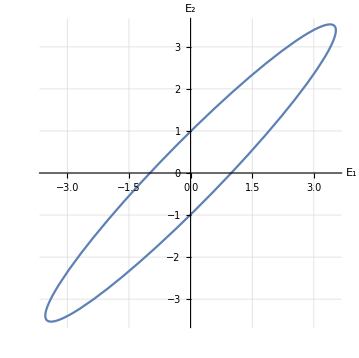

```mathematica
ParametricPlot[{{Re[e1[t]],Re[e2[t]]}},
{t,0,2π},AxesLabel->{"E_1","E_2"},GridLines->Automatic
]
```

```mathematica
equ = {
a+b == α+β,
a-b == n2/n1*(α-β),
α*Exp[I*k2*d]+β*Exp[-I*k2*d] == η*Exp[I*k3*d],
α*Exp[I*k2*d]-β*Exp[-I*k2*d] == n3/n2*η*Exp[I*k3*d]
};
s = Solve[equ,{b,α,β,η}]//Simplify
```

{{b→(a (n1 (n2+ⅇ^(2 ⅈ d k2) n2+n3-ⅇ^(2 ⅈ d k2) n3)+n2 ((-1+ⅇ^(2 ⅈ d k2)) n2-(1+ⅇ^(2 ⅈ d k2)) n3)))/(n1 (n2+ⅇ^(2 ⅈ d k2) n2+n3-ⅇ^(2 ⅈ d k2) n3)+n2 (n2-ⅇ^(2 ⅈ d k2) n2+n3+ⅇ^(2 ⅈ d k2) n3)),α→(2 a n1 (n2+n3))/(n1 (n2+ⅇ^(2 ⅈ d k2) n2+n3-ⅇ^(2 ⅈ d k2) n3)+n2 (n2-ⅇ^(2 ⅈ d k2) n2+n3+ⅇ^(2 ⅈ d k2) n3)),β→(2 a ⅇ^(2 ⅈ d k2) n1 (n2-n3))/(n1 (n2+ⅇ^(2 ⅈ d k2) n2+n3-ⅇ^(2 ⅈ d k2) n3)+n2 (n2-ⅇ^(2 ⅈ d k2) n2+n3+ⅇ^(2 ⅈ d k2) n3)),η→(4 a ⅇ^(ⅈ d (k2-k3)) n1 n2)/(n1 (n2+ⅇ^(2 ⅈ d k2) n2+n3-ⅇ^(2 ⅈ d k2) n3)+n2 (n2-ⅇ^(2 ⅈ d k2) n2+n3+ⅇ^(2 ⅈ d k2) n3))}}

```mathematica
t2 = η/.s[[1]]/.a-> 1;
fz = Numerator[t2/1];
fm = Denominator[t2/1];
t = n3/n1*ComplexExpand[(fz*Conjugate[fz])/(fm*Conjugate[fm])]//Simplify
```

(8 n1 n2^2 n3)/(4 n1 n2^2 n3+n1^2 (n2^2+n3^2)+n2^2 (n2^2+n3^2)+(n1^2-n2^2) (n2^2-n3^2) Cos[2 d k2])

```mathematica
t/.{k2-> n2*ω/c,k3-> n3*ω/c}/.{n1-> 1,n2-> 2,n3-> 3}/.{d-> 10^-6, c-> 299792458}
t/.{k2-> n2*ω/c,k3-> n3*ω/c}/.{n1-> 3,n2-> 2,n3-> 1}/.{d-> 10^-6, c-> 299792458}
t/.{k2-> n2*ω/c,k3-> n3*ω/c}/.{n1-> 2,n2-> 4,n3-> 1}/.{d-> 10^-6, c-> 299792458}
```

96/(113+15 Cos[ω/74948114500000])

96/(113+15 Cos[ω/74948114500000])

256/(468-180 Cos[ω/37474057250000])

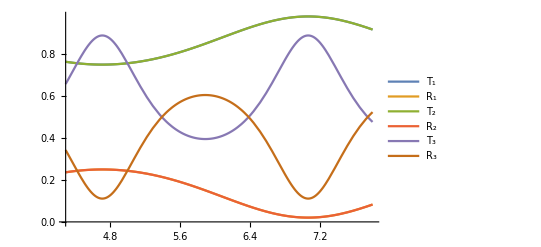

```mathematica
Plot[{96/(113+15 Cos[ω/74948114500000]),1-96/(113+15 Cos[ω/74948114500000]),96/(113+15 Cos[ω/74948114500000]),1-96/(113+15 Cos[ω/74948114500000]),256/(468-180 Cos[ω/37474057250000]),1-256/(468-180 Cos[ω/37474057250000])},{ω,4.29*10^14,7.8*10^14},
PlotLegends->{"T_1","R_1","T_2","R_2","T_3","R_3"}
]
```

```mathematica
t/.{k2-> n2*ω/c}/.{n3-> 1}
```

```mathematica
(8 n1 n2^2)/(4 n1 n2^2+n1^2 (1+n2^2)+n2^2 (1+n2^2)+(n1^2-n2^2) (-1+n2^2) Cos[(2 d n2 ω)/c])==1
```

(8 n1 n2^2)/(4 n1 n2^2+n1^2 (1+n2^2)+n2^2 (1+n2^2)+(n1^2-n2^2) (-1+n2^2) Cos[(2 d n2 ω)/c])==1

```mathematica
Solve[(8 n1 n2^2)/(4 n1 n2^2+n1^2 (1+n2^2)+n2^2 (1+n2^2)+(n1^2-n2^2) (-1+n2^2) Cos[(2 d n2 ω)/c])==1,{d,n2},Reals]
```

{{d→ConditionalExpression[-(-c π-2 c π C[1])/(2 √n1 ω),(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)],n2→ConditionalExpression[√n1,(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)]},{d→ConditionalExpression[(-c π-2 c π C[1])/(2 √n1 ω),(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)],n2→ConditionalExpression[-√n1,(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)]},{d→ConditionalExpression[-(c π-2 c π C[1])/(2 √n1 ω),(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)],n2→ConditionalExpression[√n1,(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)]},{d→ConditionalExpression[(c π-2 c π C[1])/(2 √n1 ω),(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)],n2→ConditionalExpression[-√n1,(C[1]∈ℤ&&0<n1<1)||(C[1]∈ℤ&&n1>1)]}}

```mathematica
(c π)/(2 √n1 ω)
```

(c π)/(2 √n1 ω)

```mathematica
e1x =a*Exp[I*k1*x*Cos[θ1]]+b*Exp[I*k2*x*Cos[θ1]]/.{k1-> n*ω/c,k2-> n*ω/c};
e1z =a*Exp[I*k1*z*Sin[θ1]]+b*Exp[-I*k2*z*Sin[θ1]]/.{k1-> n*ω/c,k2-> n*ω/c};
e2x =α*Exp[I*k3*x*Cos[θ2]]+β*Exp[I*k4*x*Cos[θ2]]/.{k3-> ω/c,k4-> ω/c};
e2z =α*Exp[I*k3*z*Sin[θ2]]+β*Exp[-I*k4*z*Sin[θ2]]/.{k3-> ω/c,k4-> ω/c};
e3x =η*Exp[I*k1*x*Cos[θ1]]/.{k1-> n*ω/c};
e3z =η*Exp[I*k1*z*Sin[θ1]]/.{k1-> n*ω/c};
```

```mathematica
ExpToTrig[e1z]/. n*Sin[θ1]-> 1
ExpToTrig[e2z]/.Sin[θ2]-> 1
```

a Cos[(z ω)/c]+b Cos[(z ω)/c]+ⅈ a Sin[(z ω)/c]-ⅈ b Sin[(z ω)/c]

α Cos[(z ω)/c]+β Cos[(z ω)/c]+ⅈ α Sin[(z ω)/c]-ⅈ β Sin[(z ω)/c]

```mathematica
ComplexExpand[ExpToTrig[Conjugate[e1z]]]
ComplexExpand[ExpToTrig[e1z]]
ComplexExpand[ExpToTrig[Conjugate[e2z]]]
ComplexExpand[ExpToTrig[e2z]]
```

a Cos[(n z ω Sin[θ1])/c]+b Cos[(n z ω Sin[θ1])/c]-ⅈ (a Sin[(n z ω Sin[θ1])/c]-b Sin[(n z ω Sin[θ1])/c])

a Cos[(n z ω Sin[θ1])/c]+b Cos[(n z ω Sin[θ1])/c]+ⅈ (a Sin[(n z ω Sin[θ1])/c]-b Sin[(n z ω Sin[θ1])/c])

α Cos[(z ω Sin[θ2])/c]+β Cos[(z ω Sin[θ2])/c]-ⅈ (α Sin[(z ω Sin[θ2])/c]-β Sin[(z ω Sin[θ2])/c])

α Cos[(z ω Sin[θ2])/c]+β Cos[(z ω Sin[θ2])/c]+ⅈ (α Sin[(z ω Sin[θ2])/c]-β Sin[(z ω Sin[θ2])/c])

```mathematica
D[e1x,x]
```

(ⅈ a ⅇ^((ⅈ n x ω Cos[θ1])/c) n ω Cos[θ1])/c+(ⅈ b ⅇ^((ⅈ n x ω Cos[θ1])/c) n ω Cos[θ1])/c

```mathematica
equ = {
a+b == α+β,
a-b == Cos[θ2]/(n*Cos[θ1])*(α-β),
α*Exp[I*k*λ]+β*Exp[-I*k*λ] == η*Exp[I*k1*λ],
α*Exp[I*k*λ]-β*Exp[-I*k*λ] == (n*Cos[θ1])/Cos[θ2]*η*Exp[I*k1*λ]
};
s = Solve[equ,{b,α,β,η}]//Simplify
```

{{b→(a (-1+ⅇ^(2 ⅈ k λ)) (n-Cos[θ2] Sec[θ1]) (n+Cos[θ2] Sec[θ1]))/((-1+ⅇ^(2 ⅈ k λ)) n^2-2 (1+ⅇ^(2 ⅈ k λ)) n Cos[θ2] Sec[θ1]+(-1+ⅇ^(2 ⅈ k λ)) Cos[θ2]^2 Sec[θ1]^2),α→-(2 a n (n+Cos[θ2] Sec[θ1]))/((-1+ⅇ^(2 ⅈ k λ)) n^2-2 (1+ⅇ^(2 ⅈ k λ)) n Cos[θ2] Sec[θ1]+(-1+ⅇ^(2 ⅈ k λ)) Cos[θ2]^2 Sec[θ1]^2),β→(2 a ⅇ^(2 ⅈ k λ) n (n-Cos[θ2] Sec[θ1]))/((-1+ⅇ^(2 ⅈ k λ)) n^2-2 (1+ⅇ^(2 ⅈ k λ)) n Cos[θ2] Sec[θ1]+(-1+ⅇ^(2 ⅈ k λ)) Cos[θ2]^2 Sec[θ1]^2),η→-(4 a ⅇ^(ⅈ (k-k1) λ) n Cos[θ2] Sec[θ1])/((-1+ⅇ^(2 ⅈ k λ)) n^2-2 (1+ⅇ^(2 ⅈ k λ)) n Cos[θ2] Sec[θ1]+(-1+ⅇ^(2 ⅈ k λ)) Cos[θ2]^2 Sec[θ1]^2)}}

```mathematica
t1 = η/. s[[1]]/.a-> 1
```

-(4 ⅇ^(ⅈ (k-k1) λ) n Cos[θ2] Sec[θ1])/((-1+ⅇ^(2 ⅈ k λ)) n^2-2 (1+ⅇ^(2 ⅈ k λ)) n Cos[θ2] Sec[θ1]+(-1+ⅇ^(2 ⅈ k λ)) Cos[θ2]^2 Sec[θ1]^2)

```mathematica
fz = Numerator[t1/1];
fm = Denominator[t1/1];
```

```mathematica
p1 = ComplexExpand[(fz*Conjugate[fz])/(fm*Conjugate[fm])]//Simplify
```

(128 n^2 Cos[θ1]^2 Cos[θ2]^2)/(6+24 n^2+6 n^4+8 n^2 (3+n^2) Cos[2 θ1]+2 n^4 Cos[4 θ1]+12 n^2 Cos[2 (θ1-θ2)]+8 Cos[2 θ2]+24 n^2 Cos[2 θ2]+2 Cos[4 θ2]+12 n^2 Cos[2 (θ1+θ2)]-6 Cos[2 k λ]+8 n^2 Cos[2 k λ]-6 n^4 Cos[2 k λ]-n^4 Cos[4 θ1-2 k λ]-Cos[4 θ2-2 k λ]+4 n^2 Cos[2 (θ1-k λ)]-4 n^4 Cos[2 (θ1-k λ)]-4 Cos[2 (θ2-k λ)]+4 n^2 Cos[2 (θ2-k λ)]+2 n^2 Cos[2 (θ1+θ2-k λ)]+4 n^2 Cos[2 (θ1+k λ)]-4 n^4 Cos[2 (θ1+k λ)]+2 n^2 Cos[2 (θ1-θ2+k λ)]-4 Cos[2 (θ2+k λ)]+4 n^2 Cos[2 (θ2+k λ)]+2 n^2 Cos[2 (-θ1+θ2+k λ)]+2 n^2 Cos[2 (θ1+θ2+k λ)]-n^4 Cos[4 θ1+2 k λ]-Cos[4 θ2+2 k λ])

```mathematica
p1/.{λ-> d/Cos[θ2]}/.{θ2-> ArcSin[n*Sin[θ1]]}/.{k-> 1}//Simplify
Manipulate[Plot3D[%,{d,0,2},{θ1,0,π/2},AxesLabel->{"d","θ1"}],{n,1,20}]
```

-(8 n^2 Cos[θ1]^2 (-1+n^2 Sin[θ1]^2))/(1+2 n^2+4 n^2 Cos[2 θ1]+n^4 Cos[4 θ1]-Cos[(2 √2 d)/(√(2-n^2+n^2 Cos[2 θ1]))]+2 n^2 Cos[(2 √2 d)/(√(2-n^2+n^2 Cos[2 θ1]))]-n^4 Cos[(2 √2 d)/(√(2-n^2+n^2 Cos[2 θ1]))])

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power::infy 的进一步输出将被抑制.

```mathematica
p1/.{θ2-> ArcSin[n*Sin[θ1]]}//Simplify
```

-(8 n^2 Cos[θ1]^2 (-1+n^2 Sin[θ1]^2))/(1+2 n^2+4 n^2 Cos[2 θ1]+n^4 Cos[4 θ1]-Cos[2 k λ]+2 n^2 Cos[2 k λ]-n^4 Cos[2 k λ])